```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

127

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqsW=Monitor[Simplify[Fold[And,ineqs],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts],countDone];Length[ineqsW]
```

127

```mathematica
Length[ineqsW]
```

127

```mathematica
vars=ListofVars[Select[ineqsW,Length[ListofVars[#]]==2&]]
```

{n1234,n123x4,n1234,n124x3,n1234,n12x34,n1234,n134x2,n1234,n13x24,n1234,n14x23,n1234,n1x234,n123x4,n12x3x4,n123x4,n13x2x4,n123x4,n1x23x4,n124x3,n12x3x4,n124x3,n14x2x3,n124x3,n1x24x3,n12x34,n12x3x4,n12x34,n1x2x34,n12x3x4,n1x2x3x4,n134x2,n13x2x4,n134x2,n14x2x3,n134x2,n1x2x34,n13x24,n13x2x4,n13x24,n1x24x3,n13x2x4,n1x2x3x4,n14x23,n14x2x3,n14x23,n1x23x4,n14x2x3,n1x2x3x4,n1x234,n1x23x4,n1x234,n1x24x3,n1x234,n1x2x34,n1x23x4,n1x2x3x4,n1x24x3,n1x2x3x4,n1x2x34,n1x2x3x4}

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofournull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

127

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofournull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

15

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,ineqs2],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->realnullAtomFacts],countDone];Length[ineqsW2]
```

18

```mathematica
vars2=ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]]
```

{v13x24,v13x2x4,v13x24,v1x24x3,v13x2x4,v1x2x3x4,v1x24x3,v1x2x3x4}

```mathematica
partialOrder=Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[k->ColourForKey[allGraphs,InverseNull[k]],{k,vars2}]]
```

Graph[{v1x24x3+v1x2x3x4→0,v13x24+v13x2x4→0,v13x2x4+v1x2x3x4→0,v13x24+v1x24x3→0},VertexLabels→Name,GraphLayout→LayeredDigraphEmbedding,VertexStyle→{v13x24→RGBColor[1, 0.5, 0],v13x2x4→RGBColor[1, 0.5, 0],v13x24→RGBColor[1, 0.5, 0],v1x24x3→RGBColor[1, 0.5, 0],v13x2x4→RGBColor[1, 0.5, 0],v1x2x3x4→RGBColor[1, 0.5, 0],v1x24x3→RGBColor[1, 0.5, 0],v1x2x3x4→RGBColor[1, 0.5, 0]}]

```mathematica
InverseNull[symbol_]:=First[Select[Keys[allGraphs],allGraphs[#,"colofournull"]==symbol&]]
```

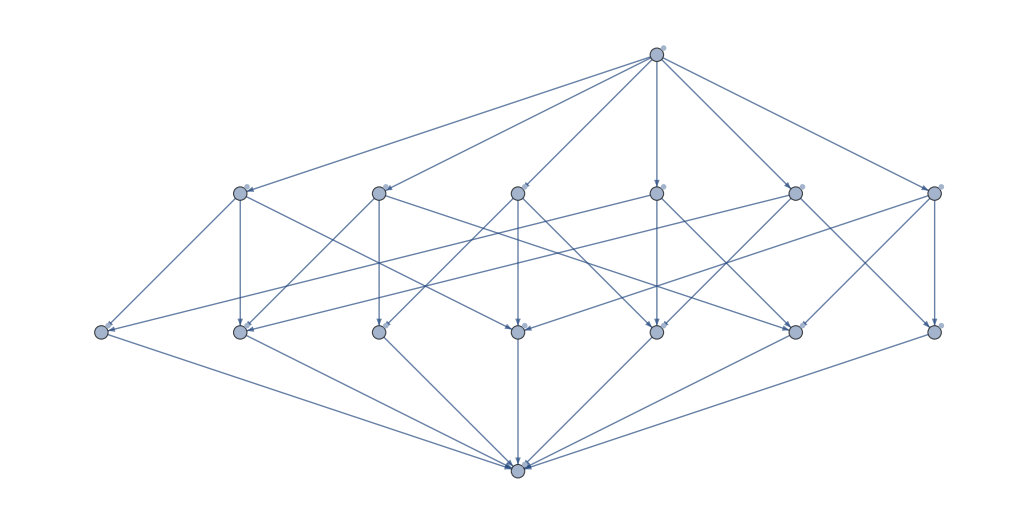

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofournull"]->allGraphs[k,"graph"],{k,nullAtomKeys}],MemberQ[vars,#[[1]]]&]]
```

Graph[{v1x24x3+v1x2x3x4→0,v13x24+v13x2x4→0,v13x2x4+v1x2x3x4→0,v13x24+v1x24x3→0},VertexLabels→{v1x2x3x4→-Graphics-,v1x24x3→-Graphics-,v13x2x4→-Graphics-,v13x24→-Graphics-}]

```mathematica
Take[ineqsW,5]
```

v1x24x3+v1x2x3x4>0&&v13x24+v13x2x4>0&&v13x2x4+v1x2x3x4>0&&v13x24+v1x24x3>0&&v13x24+v13x2x4+v1x24x3+v1x2x3x4>0

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

105

```mathematica
Take[nullAtomFacts,3]
```

{v1x2x3x4≥0,v1x2x34>0,v1x24x3≥0}

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

v1x2x3x4≥0&&v1x2x34>0&&v1x24x3≥0&&v1x23x4>0&&v1x234>0&&v14x2x3>0&&v14x23>0&&v13x2x4≥0&&v13x24≥0&&v134x2>0&&v12x3x4>0&&v12x34>0&&v124x3>0&&v123x4>0&&v1234>0

```mathematica
Monitor[Table[{p[[1]]<p[[2]]}->Length[Simplify[p[[1]]>p[[2]]&&atomFactsAnd,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts]],{p,pairs}],Position[pairs, p]]
```

{{v1x2x3x4<v1x2x34}→2,{v1x2x3x4<v1x24x3}→2,{v1x2x3x4<v1x23x4}→2,{v1x2x3x4<v1x234}→2,{v1x2x3x4<v14x2x3}→2,{v1x2x3x4<v14x23}→2,{v1x2x3x4<v13x2x4}→2,{v1x2x3x4<v13x24}→2,{v1x2x3x4<v134x2}→2,{v1x2x3x4<v12x3x4}→2,{v1x2x3x4<v12x34}→2,{v1x2x3x4<v124x3}→2,{v1x2x3x4<v123x4}→2,{v1x2x3x4<v1234}→2,{v1x2x34<v1x24x3}→2,{v1x2x34<v1x23x4}→2,{v1x2x34<v1x234}→2,{v1x2x34<v14x2x3}→2,{v1x2x34<v14x23}→2,{v1x2x34<v13x2x4}→2,{v1x2x34<v13x24}→2,{v1x2x34<v134x2}→2,{v1x2x34<v12x3x4}→2,{v1x2x34<v12x34}→2,{v1x2x34<v124x3}→2,{v1x2x34<v123x4}→2,{v1x2x34<v1234}→2,{v1x24x3<v1x23x4}→2,{v1x24x3<v1x234}→2,{v1x24x3<v14x2x3}→2,{v1x24x3<v14x23}→2,{v1x24x3<v13x2x4}→2,{v1x24x3<v13x24}→2,{v1x24x3<v134x2}→2,{v1x24x3<v12x3x4}→2,{v1x24x3<v12x34}→2,{v1x24x3<v124x3}→2,{v1x24x3<v123x4}→2,{v1x24x3<v1234}→2,{v1x23x4<v1x234}→2,{v1x23x4<v14x2x3}→2,{v1x23x4<v14x23}→2,{v1x23x4<v13x2x4}→2,{v1x23x4<v13x24}→2,{v1x23x4<v134x2}→2,{v1x23x4<v12x3x4}→2,{v1x23x4<v12x34}→2,{v1x23x4<v124x3}→2,{v1x23x4<v123x4}→2,{v1x23x4<v1234}→2,{v1x234<v14x2x3}→2,{v1x234<v14x23}→2,{v1x234<v13x2x4}→2,{v1x234<v13x24}→2,{v1x234<v134x2}→2,{v1x234<v12x3x4}→2,{v1x234<v12x34}→2,{v1x234<v124x3}→2,{v1x234<v123x4}→2,{v1x234<v1234}→2,{v14x2x3<v14x23}→2,{v14x2x3<v13x2x4}→2,{v14x2x3<v13x24}→2,{v14x2x3<v134x2}→2,{v14x2x3<v12x3x4}→2,{v14x2x3<v12x34}→2,{v14x2x3<v124x3}→2,{v14x2x3<v123x4}→2,{v14x2x3<v1234}→2,{v14x23<v13x2x4}→2,{v14x23<v13x24}→2,{v14x23<v134x2}→2,{v14x23<v12x3x4}→2,{v14x23<v12x34}→2,{v14x23<v124x3}→2,{v14x23<v123x4}→2,{v14x23<v1234}→2,{v13x2x4<v13x24}→2,{v13x2x4<v134x2}→2,{v13x2x4<v12x3x4}→2,{v13x2x4<v12x34}→2,{v13x2x4<v124x3}→2,{v13x2x4<v123x4}→2,{v13x2x4<v1234}→2,{v13x24<v134x2}→2,{v13x24<v12x3x4}→2,{v13x24<v12x34}→2,{v13x24<v124x3}→2,{v13x24<v123x4}→2,{v13x24<v1234}→2,{v134x2<v12x3x4}→2,{v134x2<v12x34}→2,{v134x2<v124x3}→2,{v134x2<v123x4}→2,{v134x2<v1234}→2,{v12x3x4<v12x34}→2,{v12x3x4<v124x3}→2,{v12x3x4<v123x4}→2,{v12x3x4<v1234}→2,{v12x34<v124x3}→2,{v12x34<v123x4}→2,{v12x34<v1234}→2,{v124x3<v123x4}→2,{v124x3<v1234}→2,{v123x4<v1234}→2}

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Total//Expand],#]&]
```

{v1x2x3x4,v1x2x34,v1x24x3,v1x23x4,v1x234,v14x2x3,v14x23,v13x2x4,v13x24,v134x2,v12x3x4,v12x34,v124x3,v123x4,v1234}

```mathematica
Select[Keys[allGraphs],allGraphs[#,"colofournull"]==p1x2x3x4x5&]
```

{}

```mathematica
allGraphs[0,"graph"]
```

-Graphics-

```mathematica
allGraphs[quad1Key,"colofournull"]/.repcolofournullgraph2//Expand//Length
```

2

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total//Expand],#]&]
```

{v1x2x3x4,v1x2x34,v1x24x3,v1x23x4,v1x234,v14x2x3,v14x23,v13x2x4,v13x24,v134x2,v12x3x4,v12x34,v124x3,v123x4,v1234}

```mathematica
Select[Keys[allGraphs],MemberQ[{p1x2x3x4x5,p1x25x34,p15x24x3,p14x23x5,p13x2x45,p12x35x4},allGraphs[#,"colofournull"]]&]
```

{}

```mathematica
allGraphs[6562,"graph"]
```

Missing[KeyAbsent,6562]